#### Радиально - базисные нейронные сети

```mathematica
ClearAll[f,f2d,c1,c2,x1,x2];
```

```mathematica
xmax=4;
crange=6;
f[x_,c_,sigma_]:=Exp[-(x-c)^2/(2*sigma^2)];
frsqr[x_,c_,sigma_]:=1/(1+(x*sigma)^2)-c;
frmsqr[x_,c_,sigma_]:=1/Sqrt[(1+(x*sigma-c)^2)];
```

Одномерная функция

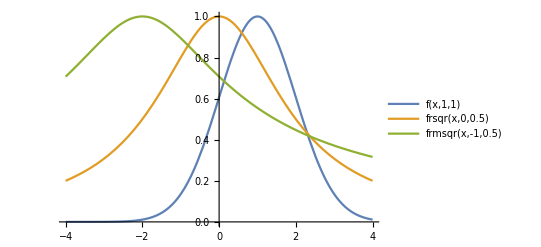

```mathematica
Plot[{f[x,1,1],frsqr[x,0,0.5], frmsqr[x,-1,0.5]},{x,-xmax,xmax}, PlotLegends->"Expressions"]
```

Двумерная функция

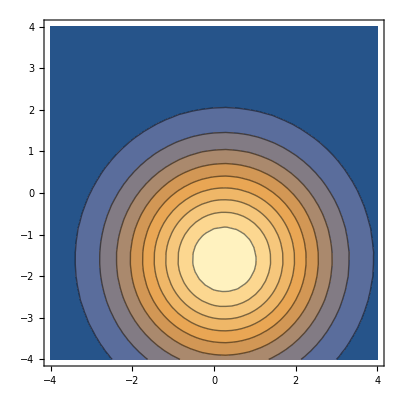

```mathematica
f2d[x1_,x2_,c1_, c2_, sigma_]:=Exp[-((x1-c1)^2+(x2-c2)^2)/(2*sigma^2)];
bx=RandomReal[{-crange,crange}]; by=RandomReal[{-crange,crange}];
ContourPlot[f2d[x1,x2, bx, by,1.7],{x1,-xmax,xmax},{x2,-xmax,xmax}]
```

Сумма функций

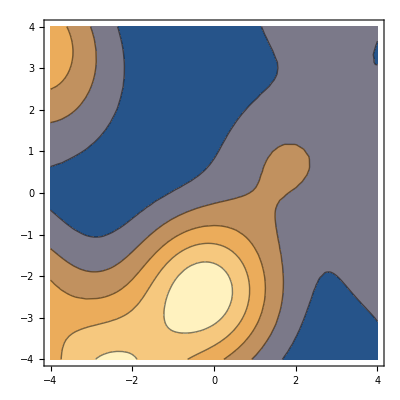
{-Graphics-,-Graphics3D-}

```mathematica
count = 16;
c1=Table[RandomReal[{-crange,crange}],{i,1,count}];
c2=Table[RandomReal[{-crange,crange}],{i,1,count}];
s=Table[RandomReal[{0.9,1.5}],{i,1,count}];
bias = 1;
fsum = Sum[f2d[x1,x2, c1[[i]], c2[[i]],s[[i]]],{i,1,count}]-bias;
{ContourPlot[fsum,{x1,-xmax,xmax},{x2,-xmax,xmax}], Plot3D[fsum,{x1,-xmax,xmax},{x2,-xmax,xmax}]}
```

Область над плосткостью отсечения

```mathematica
Manipulate[RegionPlot[fsum>high,{x1,-xmax,xmax},{x2,-xmax,xmax}], {high,-8, 8, 0.1}]
```

General::munfl: Exp[-890.033] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1104.82] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.653] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-890.033] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1104.82] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.653] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Сигмоидальная функция

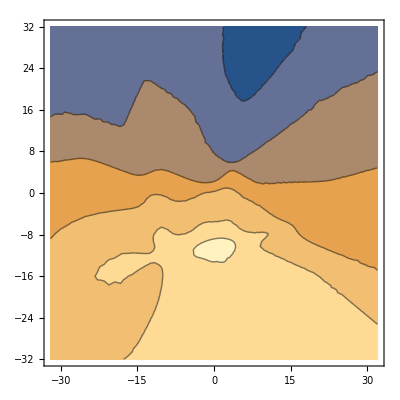
{-Graphics-,-Graphics3D-}

```mathematica
(**c1=Table[RandomReal[{-crange,crange}],{i,1,count}]; c2=Table[RandomReal[{-crange,crange}],{i,1,count}];**)
w1=Table[RandomReal[{-1,1}],{i,1,count}]; w2=Table[RandomReal[{-1,1}],{i,1,count}];
fsigm2d[x1_,x2_,c1_,c2_,w1_,w2_, sigma_]:= 1/(1+Exp[-(w1*x1-c1+w2*x2-c2)*sigma]);
xmax = 32;
fsigmsum=Sum[fsigm2d[x1,x2, c1[[i]], c2[[i]], w1[[i]],w2[[i]],2],{i,1,count}];
{ContourPlot[fsigmsum,{x1,-xmax,xmax},{x2,-xmax,xmax}],Plot3D[fsigmsum,{x1,-xmax,xmax},{x2,-xmax,xmax}]}
```

```mathematica
Manipulate[RegionPlot[fsigmsum>high,{x1,-xmax,xmax},{x2,-xmax,xmax}], {high, -8,8}]
```